## Set all data for all simulations

```mathematica
<<(NotebookDirectory[]<>"tmp.mx")
```

```mathematica
Nϵ0=1 10^-7;
Nσ0=1/100;

precResult=5;
ωbar=10^5;
MaxExtraPrecision=1000;

Nsub={ϵ0->Nϵ0,σ0->Nσ0};
Clear[tmp1,tmp2,tmp3,tmp4,tmp5,tmp6,tmp7,tmp8,tmp9,tmp10]
```

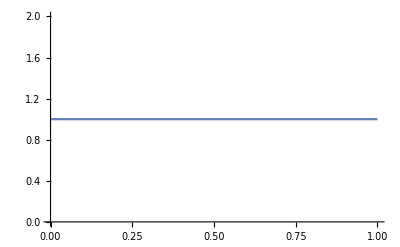

```mathematica
G[ω_]:=1-ⅇ^(Nϵ0(2-ω))
G[ω_]:=1
Plot[G[ω],{ω,2,10/Nϵ0},PlotRange->All]
```

```mathematica
h=Nϵ0/100;

Dsummand2[x_,n_]:=Piecewise[{{summand2//.{ω->x},n==0},{h^-n Sum[(-1)^i Binomial[n,i](summand2//.{ω->x+(n/2-i)h}),{i,0,n}],n≠0}}]
Dsummand2derσ0[x_,n_]:=Piecewise[{{summand2derσ0//.{ω->x},n==0},{h^-n Sum[(-1)^i Binomial[n,i](summand2derσ0//.{ω->x+(n/2-i)h}),{i,0,n}],n≠0}}]
```

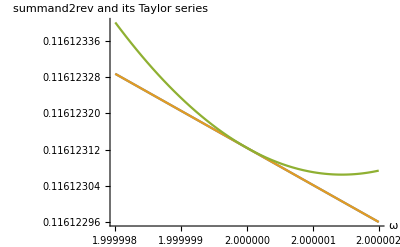

```mathematica
xmin=2-20 Nϵ0;
xder=2;
xmax=2+20 Nϵ0;

Plot[{Dsummand2[x,0]/.Nsub,Dsummand2[xder,0]+(x-xder) Dsummand2[xder,1]/.Nsub,Dsummand2[xder,0]+(x-xder) Dsummand2[xder,1]+(x-xder)^2/2 Dsummand2[xder,2]/.Nsub},{x,xmin,xmax},AxesLabel->{"ω","summand2rev and its Taylor series"}]

Clear[xmin,xder,xmax]
```

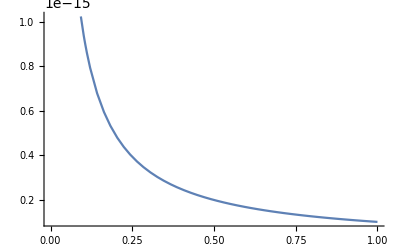

```mathematica
plotPrec=30;

Plot[summand2/.Nsub,{ω,2,Round[100/Nϵ0]},WorkingPrecision->plotPrec]

Clear[plotPrec]
```

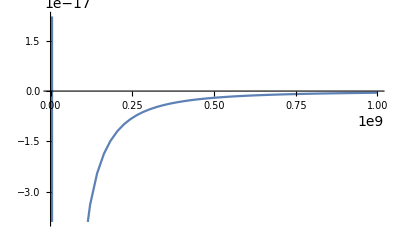

```mathematica
plotPrec=30;

Plot[summand2-Sum[summand2leading[i]/ω^i,{i,order}]/.Nsub,{ω,2,Round[100/Nϵ0]},WorkingPrecision->plotPrec]

Clear[plotPrec]
```

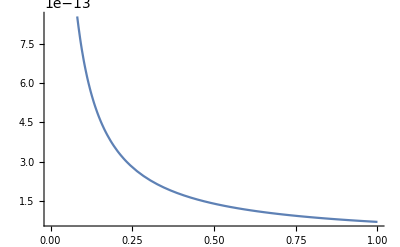

```mathematica
plotPrec=MachinePrecision;

Plot[Sum[summand2leading[i]/ω^i,{i,order}]/.Nsub,{ω,2,Round[100/Nϵ0]},WorkingPrecision->plotPrec]

Clear[plotPrec]
```

## Evaluate log((Z_(1-loop)(σ_0))/(Z_(1-loop)(∞))) (my formula no. 1)

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp1=summand1/.Nsub//N[#,{∞,20}]&

tmp2=NIntegrate[summand2/.Nsub,{ω,2,ωbar},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

6.2818365847636743178

$Aborted

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp3=NIntegrate[summand2-Sum[summand2leading[i]/ω^i,{i,order}]/.Nsub,{ω,ωbar,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

6.04051311×10^-11

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp4=-(χv-χvcir)Log[ωbar]-Sum[summand2leading[i]/(1-i)ωbar^(1-i),{i,2,order}]/.Nsub//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

-9.100067089×10^-10

```mathematica
p=3;
mytmp=Dsummand2[x,2p];

$MaxExtraPrecision=MaxExtraPrecision;

tmp5=-(summand2/.ω->2)/2-Sum[BernoulliB[2k]/((2k)!)Dsummand2[2,2k-1],{k,1,p}]-NIntegrate[mytmp  BernoulliB[2p,IntegerPart[x]]/((2p)!)/.Nsub,{x,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]/.Nsub //N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

-0.0513934752016054221

```mathematica
tmp1+tmp2+tmp3+tmp4+tmp5//N[#,{∞, precResult}]&
-3/2 Log[Tanh[Nσ0]]-1/2 Log[1+ⅇ^(-2Nσ0)]//N[#,{∞,precResult}]&
```

0.00009

0.0001

## Evaluate log((Z_(1-loop)(σ_0))/(Z_(1-loop)(∞))) (my formula no. 2) [used in paper with G=1]

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp1=summand1/.Nsub//N[#,{∞,20}]&

tmp2=NIntegrate[summand2-(χv-χvcir)/ω-Sum[G[ω] summand2leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

6.2818365847636743178

0.335747200092467115

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp3=-(χv-χvcir)Log[2]/.Nsub//N[#,{∞,20}]&
tmp4=NIntegrate[Sum[G[ω] summand2leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

-6.93077868383×10^-8

0.

```mathematica
p=3;
mytmp=Dsummand2[x,2p];

$MaxExtraPrecision=MaxExtraPrecision;

tmp5=-(summand2/.ω->2)/2-Sum[BernoulliB[2k]/((2k)!)Dsummand2[2,2k-1],{k,1,p}]-NIntegrate[mytmp  BernoulliB[2p,IntegerPart[x]]/((2p)!)/.Nsub,{x,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]/.Nsub //N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

-0.0513943748462277479

```mathematica
tmp1+tmp2+tmp3+tmp4+tmp5//N[#,{∞, precResult}]&
-3/2 Log[Tanh[Nσ0]]-1/2 Log[1+ⅇ^(-2Nσ0)]//N[#,{∞,precResult}]&
```

6.5662

6.5662

## Create list for cell above

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

For[Nσ0=1/100,Nσ0≤501/100,Nσ0=Nσ0+5/100,

Nsub={ϵ0->Nϵ0,σ0->Nσ0};

tmp1=summand1/.Nsub//N[#,{∞,20}]&;

tmp2=NIntegrate[summand2-(χv-χvcir)/ω-Sum[G[ω] summand2leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&;

tmp3=-(χv-χvcir)Log[2]/.Nsub//N[#,{∞,20}]&;
tmp4=NIntegrate[Sum[G[ω] summand2leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&;

p=3;
mytmp=Dsummand2[x,2p];

tmp5=-(summand2/.ω->2)/2-Sum[BernoulliB[2k]/((2k)!)Dsummand2[2,2k-1],{k,1,p}]-NIntegrate[mytmp  BernoulliB[2p,IntegerPart[x]]/((2p)!)/.Nsub,{x,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]/.Nsub //N[#,{∞,20}]&;

Print[{Nσ0,tmp1+tmp2+tmp3+tmp4+tmp5,(-3/2 Log[Tanh[Nσ0]]-1/2 Log[1+ⅇ^(-2Nσ0)]),tmp1+tmp2+tmp3+tmp4+tmp5-(-3/2 Log[Tanh[Nσ0]]-1/2 Log[1+ⅇ^(-2Nσ0)])}//N[#,{∞,precResult}]&]
]

$MaxExtraPrecision=50;
```

{0.01,6.5662,6.5662,-0.00002}

{0.06,3.9044,3.9044,0.}

{0.11,3.0223,3.0224,0.}

{0.16,2.4886,2.4886,0.}

{0.21,2.1103,2.1103,0.}

{0.26,1.8206,1.8206,0.}

{0.31,1.5885,1.5886,0.}

{0.36,1.3971,1.3971,0.}

{0.41,1.2358,1.2358,0.}

{0.46,1.098,1.098,0.}

{0.51,0.9787,0.9787,0.}

{0.56,0.8748,0.8748,0.}

{0.61,0.7835,0.7835,0.}

{0.66,0.7029,0.7029,0.}

{0.71,0.6315,0.6315,0.}

{0.76,0.568,0.568,0.}

{0.81,0.5113,0.5113,0.}

{0.86,0.4607,0.4607,0.}

{0.91,0.4153,0.4153,0.}

{0.96,0.3746,0.3746,0.}

{1.01,0.338,0.338,0.}

{1.06,0.3052,0.3052,0.}

{1.11,0.2756,0.2756,0.}

{1.16,0.2489,0.2489,0.}

{1.21,0.2249,0.2249,0.}

{1.26,0.2032,0.2032,0.}

{1.31,0.1837,0.1837,0.}

{1.36,0.166,0.166,0.}

{1.41,0.1501,0.1501,0.}

{1.46,0.1357,0.1357,0.}

{1.51,0.1227,0.1227,0.}

{1.56,0.111,0.111,0.}

{1.61,0.1003,0.1003,0.}

{1.66,0.0907,0.0907,0.}

{1.71,0.0821,0.0821,0.}

{1.76,0.0742,0.0742,0.}

{1.81,0.0672,0.0672,0.}

{1.86,0.0607,0.0607,0.}

{1.91,0.0549,0.0549,0.}

{1.96,0.0497,0.0497,0.}

{2.01,0.045,0.045,0.}

{2.06,0.0407,0.0407,0.}

{2.11,0.0368,0.0368,0.}

{2.16,0.0333,0.0333,0.}

{2.21,0.0301,0.0301,0.}

{2.26,0.0273,0.0273,0.}

{2.31,0.0247,0.0247,0.}

{2.36,0.0223,0.0223,0.}

{2.41,0.0202,0.0202,0.}

{2.46,0.0183,0.0183,0.}

{2.51,0.0165,0.0165,0.}

{2.56,0.0149,0.0149,0.}

{2.61,0.0135,0.0135,0.}

{2.66,0.0122,0.0122,0.}

{2.71,0.0111,0.0111,0.}

{2.76,0.01,0.01,0.}

{2.81,0.0091,0.0091,0.}

{2.86,0.0082,0.0082,0.}

{2.91,0.0074,0.0074,0.}

{2.96,0.0067,0.0067,0.}

{3.01,0.0061,0.0061,0.}

{3.06,0.0055,0.0055,0.}

{3.11,0.005,0.005,0.}

{3.16,0.0045,0.0045,0.}

{3.21,0.0041,0.0041,0.}

{3.26,0.0037,0.0037,0.}

{3.31,0.0033,0.0033,0.}

{3.36,0.003,0.003,0.}

{3.41,0.0027,0.0027,0.}

{3.46,0.0025,0.0025,0.}

{3.51,0.0022,0.0022,0.}

{3.56,0.002,0.002,0.}

{3.61,0.0018,0.0018,0.}

{3.66,0.0017,0.0017,0.}

{3.71,0.0015,0.0015,0.}

{3.76,0.0014,0.0014,0.}

{3.81,0.0012,0.0012,0.}

{3.86,0.0011,0.0011,0.}

{3.91,0.001,0.001,0.}

{3.96,0.0009,0.0009,0.}

{4.01,0.0008,0.0008,0.}

{4.06,0.0007,0.0007,0.}

{4.11,0.0007,0.0007,0.}

{4.16,0.0006,0.0006,0.}

{4.21,0.0006,0.0006,0.}

{4.26,0.0005,0.0005,0.}

{4.31,0.0005,0.0005,0.}

{4.36,0.0004,0.0004,0.}

{4.41,0.0004,0.0004,0.}

{4.46,0.0003,0.0003,0.}

{4.51,0.0003,0.0003,0.}

{4.56,0.0003,0.0003,0.}

{4.61,0.0002,0.0002,0.}

{4.66,0.0002,0.0002,0.}

{4.71,0.0002,0.0002,0.}

{4.76,0.0002,0.0002,0.}

{4.81,0.0002,0.0002,0.}

{4.86,0.0002,0.0002,0.}

{4.91,0.0001,0.0001,0.}

{4.96,0.0001,0.0001,0.}

{5.01,0.0001,0.0001,0.}

## Evaluate d/dσ_0log((Z_(1-loop)(σ_0))/(Z_(1-loop)(∞))) (my formula no. 2der)

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp1=summand1derσ0/.Nsub//N[#,{∞,20}]&

tmp2=NIntegrate[summand2derσ0-Simplify[D[χv,σ0]]/ω-Sum[G[ω] summand2derσ0leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

-0.0001816048701801644

-0.0000522395990925152

```mathematica
$MaxExtraPrecision=MaxExtraPrecision;

tmp3=-Simplify[D[χv,σ0]]Log[2]/.Nsub//N[#,{∞,20}]&
tmp4=NIntegrate[Sum[G[ω] summand2derσ0leading[i]/ω^i,{i,2,order}]/.Nsub,{ω,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]//N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

2.51705×10^-13

1.2569013×10^-12

```mathematica
p=4;
mytmp=Dsummand2derσ0[x,2p];

$MaxExtraPrecision=MaxExtraPrecision;

tmp5=-(summand2derσ0/.ω->2)/2-Sum[BernoulliB[2k]/((2k)!)Dsummand2derσ0[2,2k-1],{k,1,p}]-NIntegrate[mytmp  BernoulliB[2p,IntegerPart[x]]/((2p)!)/.Nsub,{x,2,∞},WorkingPrecision->50,AccuracyGoal->precResult,PrecisionGoal->precResult]/.Nsub //N[#,{∞,20}]&

$MaxExtraPrecision=50;
```

6.8427927247249×10^-6

```mathematica
tmp1+tmp2+tmp3+tmp4+tmp5//N[#,{∞, precResult}]&
D[-3/2 Log[Tanh[σ0]]-1/2 Log[1+ⅇ^(-2σ0)],σ0]/.Nsub//N[#,{∞,precResult}]&
```

-0.0002

-0.0003

## Prove the ϵ-limit BEFORE ω-summing gives you the same

```mathematica
tmp1=Series[summand1,{ϵ0,0,0},Assumptions->ϵ0>0];
tmp1=Exp[tmp1]//Normal//TrigToExp//Simplify//PowerExpand
```

(ⅇ^σ0+2 ⅇ^(3 σ0))/(2 (-1+ⅇ^(2 σ0))^(3/2))

```mathematica
tmp2=Series[summand2,{ϵ0,0,0},Assumptions->ϵ0>0];
tmp2=Exp[tmp2]//Normal//TrigToExp//Simplify//PowerExpand
```

((1+ω) (ω+ⅇ^(2 σ0) (2+ω)))/((2+ω) (-1+ω+ⅇ^(2 σ0) (1+ω)))

```mathematica
tmp2=Product[tmp2,{ω,3,Λ}]//PowerExpand//Simplify//Series[#,{Λ,∞,0}]&//Normal
```

(2 (1+ⅇ^(2 σ0)))/(1+2 ⅇ^(2 σ0))

```mathematica
((tmp1 tmp2)/(Tanh[σ0]^(-3/2)/(√(1+ⅇ^(-2σ0)))))^2//Simplify
```

1

## Prove the μ-sum is zero since summand ~ # μ ϵ^(-μ ω)/ω^2

```mathematica
tmp={LerchPhi[z_,s_,a_]:>Sign[a] (1/(a^s (1-z))-(a^(-1-s) s z)/(1-z)^2+(a^(-2-s) s (1+s) (z+z^2))/(2 (1-z)^3)-(a^(-3-s) s (1+s) (2+s) (z+4 z^2+z^3))/(6 (1-z)^4))};

tmp=-μ/2 ⅇ^(-ω μ)(Log[(Refine[fermfactor[ω+1/2]/fermfactorcir[ω+1/2] fermfactorcir[ω-1/2]/fermfactor[ω-1/2],Assumptions->ω≥3])]/.tmp//Series[#,{ω,∞,2},Assumptions->ω>0]&//Normal);
```

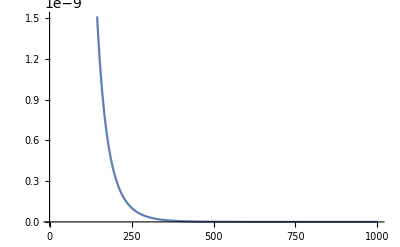

```mathematica
plotPrec=18;

Nμ=10^-2;
Plot[summand5-tmp/.{μ->Nμ}/.Nsub,{ω,3,10/Nμ},WorkingPrecision->plotPrec]

Clear[plotPrec]
```